## Construction of LHCb bound

Beyond the tabulated range, the bound on the branching ratio is assumed to stay constant for very small lifetimes and to increase linearly for very large lifetimes.

### B → K*A

```mathematica
pstos=10^-12
LogKstarBRInter=Interpolation[Log[10,{#[[1]],#[[2]],#[[3]]}&/@Import[FileNameJoin[{NotebookDirectory[],"auxiliary data/lhcbkstar.txt"}],"Data"]],InterpolationOrder->1];
KstarBRInter[m_,τ_]:=LogKstarBRInter[Log[10,m]+3,Log[10,τ]]
KstarBRboundTemp[m_,τ_]:=Piecewise[{{KstarBRInter[m,Max[τ,0.1]],τ≤1000&&m≥0.214&&m≤4.349},{KstarBRInter[m,1000]*τ/1000,τ>1000&&m≥0.214&&m≤4.349}},1]
(*From ps to s*)
LHCbBRbound["K^*",m_,τ_]=KstarBRboundTemp[m,pstos^-1*τ];
```

1/1000000000000

### B → KA

```mathematica
KBRInter=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"auxiliary data/lhcbk.dat"}],"Data"],InterpolationOrder->1];
KBRboundTemp[m_,τ_] :=Piecewise[{{KBRInter[m,Max[Log[10,τ],-1]],Log[10,τ]≤ 2 && m≥ 0.25 && m< 0.89},{KBRInter[m,2]+Log[10,τ] -2, Log[10,τ]>2 && m≥ 0.25 && m< 0.89},{KBRInter[m,Max[Log[10,τ],-1]],Log[10,τ]≤ 3 && m≥ 0.89 && m≤ 4.7},{KBRInter[m,3]+Log[10,τ] -3, Log[10,τ]>3 && m≥ 0.89 && m≤ 4.7}},0]
(*From ps to s*)
LHCbBRbound["K^+",m_,τ_]=KBRboundTemp[m,pstos^-1*τ];
```

## Plot

```mathematica
DensityPlot[KstarBRboundTemp[m,10^logτ],{m,0.22,4.265},{logτ,-1,3},ColorFunction->ColorData[{"Rainbow","Reverse"}],ColorFunctionScaling->True,PlotRange->{{0.22,4.265},{-1,3},{-10,-6}},PlotLegends->Placed[Automatic,Right],AspectRatio->0.4,ImageSize->400,PlotPoints->100]
```

-Graphics-

```mathematica
DensityPlot[KBRboundTemp[m,10^logτ],{m,0.25,4.7},{logτ,-1,3},ColorFunction->ColorData[{"Rainbow","Reverse"}],ColorFunctionScaling->True,PlotRange->{{0.25,4.7},{-1,3},{-10,-6.8}},PlotLegends->Placed[Automatic,Right],AspectRatio->0.4,ImageSize->400,PlotPoints->100]
```

-Graphics-

Note that the bound given by LHCb for masses around 4.2 GeV and large lifetimes is not included in the data table.

## ALP-fermion case

### Data importing

{ma GeV,Br_Kplus,Br_K0star,Br_K1,Br_K2star,Br_Kstar892,Br_Kstar1410,Br_Kstar1680,Br_Piplus,Br_Total,P_B->a,FNAL (DUNE),P_B->a,SPS (SHiP),P_B->a,LHC}

12

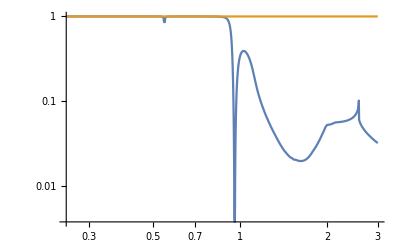

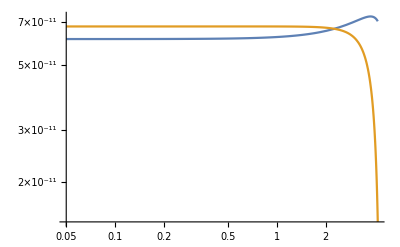

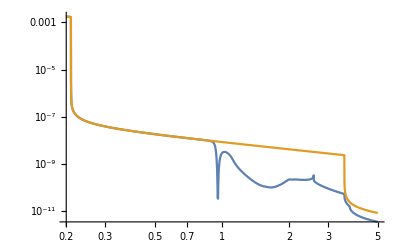

```mathematica
vh=246;
data=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/branching ratios/ProdProbabilitiesFromB-model-Fermion universal-Lambda-1.-TeV.csv"}],"csv"];
data[[1]]
(*y = 2Subscript[v, h]/f*)
BrBtoALP["K^+",ma_,y_]=(1/(2vh))^2 y^2 Interpolation[Drop[data,1][[All,{1,2}]],InterpolationOrder->1][ma];
BrBtoALP["K^*",ma_,y_]=(1/(2vh))^2 y^2 Interpolation[Drop[data,1][[All,{1,6}]],InterpolationOrder->1][ma];
DecayWidthsALPs=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/decay widths/Widths-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
processes=DecayWidthsALPs[[4]][[1]];
Positionμ=Position[processes,"2μ"][[1]][[1]]
widthtsdata=Drop[DecayWidthsALPs[[4]],3];
ΓALPtot["New",ma_,y_]=(1/(2vh))^2 y^2 Interpolation[widthtsdata[[All,{1,-1}]],InterpolationOrder->1][ma];
ΓALP["PBC",ma_,y_]=(1/(2vh))^2 y^2 Interpolation[Join[widthtsdata[[All,{1}]],widthtsdata[[All,{Position[processes,"2e"][[1]][[1]]}]]+widthtsdata[[All,{Position[processes,"2μ"][[1]][[1]]}]]+widthtsdata[[All,{Position[processes,"2τ"][[1]][[1]]}]],2],InterpolationOrder->1][ma];
τALP["New",ma_,y_]=(6.58*10^-25)/ΓALPtot["New",ma,y];
τALP["PBC",ma_,y_]=(6.58*10^-25)/ΓALP["PBC",ma,y];
ΓALPμμ[ma_,y_]=(1/(2vh))^2 y^2 Interpolation[widthtsdata[[All,{1,Position[processes,"2μ"][[1]][[1]]}]],InterpolationOrder->1][ma];
BrALPμμ["New",ma_]=ΓALPμμ[ma,1]/ΓALPtot["New",ma,1];
BrALPμμ["PBC",ma_]=ΓALPμμ[ma,1]/ΓALP["PBC",ma,1];
LogLogPlot[{BrALPμμ["New",ma],BrALPμμ["PBC",ma]},{ma,0.25,3}]
LogLogPlot[{BrBtoALP["K^+",ma,10^-5],BrBtoALP["K^*",ma,10^-5]},{ma,0.05,4.2},PlotRange->All]
LogLogPlot[{τALP["New",ma,10^-4],τALP["PBC",ma,10^-4]},{ma,0.2,5}]
```

### Producing the bounds

```mathematica
{ymin[τA_,ma_],ymax[τA_,ma_]}:=(*{1.01 √(τA[ma,1]/(1.3*10^-9)),0.99 √(τA[ma,1]/10^-13.)}*){10^-4,1}
fboundLHCbTempOld[ma_,Ktype_,Pheno_]:=If[!(ma<=0.21||0.38≤ ma≤0.51||2.9≤ma≤3.2||3.5≤ma≤3.85||0.948<ma<0.97||0.54<ma<0.557||ma==0.135),10^(y/.FindRoot[Log10[(BrBtoALP[Ktype,ma,10^y]*BrALPμμ[Pheno,ma])/(10^LHCbBRbound[Ktype,ma,τALP[Pheno,ma,10^y]]+10^-90.)]==0,{y,(Log10[Max[ymin[τALP,ma],√(τALP[Pheno,ma,1]/(5*10^-9))]]+Log10[ymax[τALP,ma]])/2,Log10[Max[ymin[τALP,ma],√(τALP[Pheno,ma,1]/(5*10^-9))]],Log10[ymax[τALP,ma]]}]),1]
fboundLHCbTemp[ma_,Ktype_,Pheno_]:=Block[{},
If[!(ma<=0.21||0.38≤ ma≤0.51||2.9≤ma≤3.2||3.6≤ma≤3.85||0.948<ma<0.97||0.54<ma<0.557||ma==0.135),tabb0=Quiet[Table[{10^y,Quiet[Abs[Log10[(BrBtoALP[Ktype,ma,10^y]*BrALPμμ[Pheno,ma])/(10^LHCbBRbound[Ktype,ma,τALP[Pheno,ma,10^y]]+10^-90.)]]]},{y,Log10[Max[ymin[τALP,ma],√(τALP[Pheno,ma,1]/(5*10^-9))]],Log10[ymax[τALP,ma]],(Log10[ymax[τALP,ma]]-Log10[Max[ymin[τALP,ma],√(τALP[Pheno,ma,1]/(5*10^-9))]])/300}]];
vall=SortBy[tabb0,#[[2]]&][[1]]//N,
vall={1,0.}];
Join[{ma},vall]
]
Do[LHCbboundsALP[Ktype,Pheno]=ParallelTable[Quiet[fboundLHCbTemp[ma,Ktype,Pheno]],{ma,0.28,4.65,0.02}],{Ktype,{"K^+","K^*"}},{Pheno,{"New","PBC"}}]
(*rescaledKplusOld={#[[1]],#[[2]]*√(BrALPμμ["PBC",#[[1]]]/BrALPμμ["New",#[[1]]])}&/@LHCbboundsALP["K^+","PBC"];*)
```

{Null,Null}

#### Test

```mathematica
fboundLHCbTempOld[2.8,"K^+","PBC"]//AbsoluteTiming
fboundLHCbTemp[2.8,"K^+","PBC"]//AbsoluteTiming
```

{0.195997,0.000121036}

{0.0170879,{2.8,0.000120226,0.0116569}}

### Plots

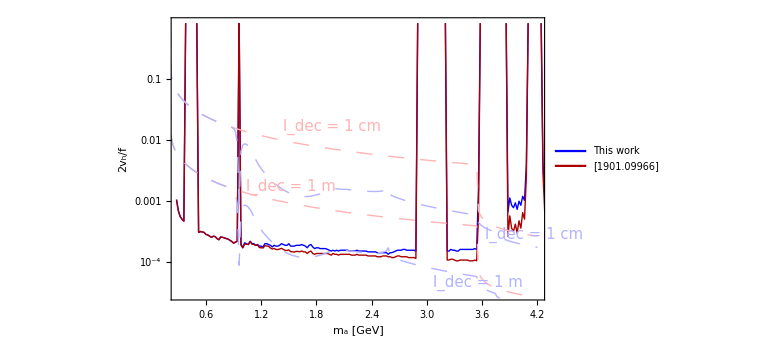

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\LHCb-constraints.pdf

Export::nodir: Directory C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\bounds\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\bounds\bounds-LHCb-Fermion universal.dat.

$Failed

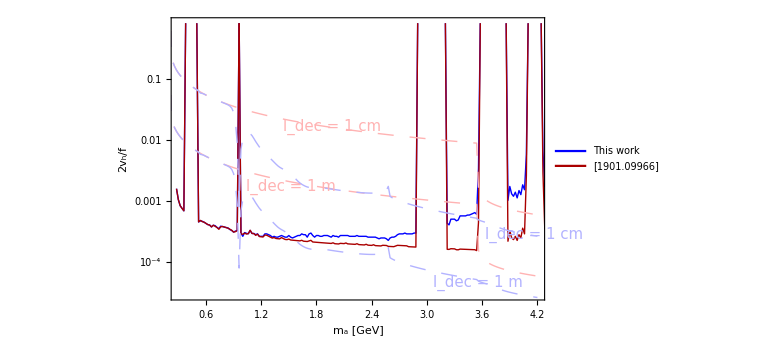

C:\Users\miksi\Dropbox\Science 2\ALP-fermion project\TBC\plots\LHCb-constraints.pdf

-Graphics-

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\LHCb-constraints.pdf

Part::partd: Part specification LHCbboundsALP(Ktype,Pheno)⟦All,{1,2}⟧ is longer than depth of object.

Export::chtype: First argument FileNameJoin[{NotebookDirectory,bounds,bounds-LHCb-Fermion universal.dat}] is not a valid file specification.

$Failed

```mathematica
plotlhcb=Show[ListLogPlot[Evaluate[Join[Flatten[Table[Select[LHCbboundsALP[Ktype,Pheno][[All,{1,2}]],!(0.79<#[[1]]<0.83&&#[[1]])&],{Ktype,{"K^+"}},{Pheno,{"New","PBC"}}],1]]],Joined->True,PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Red,Dashing[0.02]},{Thick, Lighter@Lighter@Red},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Green},{Thick,Darker@Green,Dashing[0.01]},{Thick,Black},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"m_a [GeV]" , "2v_h/f"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.3,4.2},{0.3*10^-4,0.8}}(*,PlotLabel->Style[{""},22,Black]*),Filling->{11->{Bottom,Directive[Gray,Opacity[0.3]]},12->{Bottom,Directive[Gray,Opacity[0.3]]},13->{Bottom,Directive[Gray,Opacity[0.3]]}}],LogLogPlot[{10+x,10+x,10+x,10+x,10+x},{x,0.05,10},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Red},{Thick, Lighter@Lighter@Red}},PlotLegends->Placed[Style[#,16]&/@{"This work","[1901.09966]"},{0.17,0.07}]],ListLogPlot[{Table[{ma,√((3*10^8*τALP["PBC",ma,1]*80/ma)/0.01)},{ma,0.2,4.2,0.02}],Table[{ma,√((3*10^8*τALP["PBC",ma,1]*80/ma)/1)},{ma,0.2,4.2,0.02}],Table[{ma,√((3*10^8*τALP["New",ma,1]*80/ma)/0.01)},{ma,0.2,4.2,0.02}],Table[{ma,√((3*10^8*τALP["New",ma,1]*80/ma)/1)},{ma,0.2,4.2,0.02}]},PlotStyle->{{Thick,Lighter@Lighter@Lighter@Red,Dashing[0.02]},{Thick,Lighter@Lighter@Lighter@Red,Dashing[0.02]},{Thick,Lighter@Lighter@Lighter@Blue,Dashing[0.02]},{Thick,Lighter@Lighter@Lighter@Blue,Dashing[0.02]}},Joined->True],Graphics[{Text[Style["l_dec = 1 cm",15,Lighter@Lighter@Lighter@Red],Scaled[{0.3,0.615}],Left,{3,-0.42}],Text[Style["l_dec = 1 m",15,Lighter@Lighter@Lighter@Red],Scaled[{0.2,0.4}],Left,{3,-0.35}],Text[Style["l_dec = 1 cm",15,Lighter@Lighter@Lighter@Blue],Scaled[{0.84,0.23}],Left,{3,-0.6}],Text[Style["l_dec = 1 m",15,Lighter@Lighter@Lighter@Blue],Scaled[{0.7,0.06}],Left,{3,-0.5}]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/LHCb-constraints.pdf"}],plotlhcb]
Export[FileNameJoin[{NotebookDirectory[],"bounds","bounds-LHCb-Fermion universal.dat"}],LHCbboundsALP["K^+","New"][[All,{1,2}]],"Table"]
```